```mathematica
Clear["Global`*"];
```

```mathematica
QQ=10^-9;(*C*)
ϵ0=8.85×10^-12;(*F/m*)
```

```mathematica
t0=SessionTime[];
```

```mathematica
Geometry={Disk[],Rectangle[{1,2},{7,4}],Triangle[{{3,0},{6,1},{2,-1.5}}]};
HighlightMesh[bMesh=BoundaryMesh[DiscretizeRegion[RegionUnion@@Geometry,MaxCellMeasure->0.001]],Labeled[0,"Index"]]
NEl=MeshCellCount[%,1]
```

-Graphics-

680

```mathematica
GreenF[x_,x0_]:=-N[1/(2 π) Log[Norm[x-x0]]];
DGreenF[x_,x0_]:=-N[1/(2 π Norm[x-x0])];
```

```mathematica
BElts=MeshPrimitives[bMesh,1];
Knots=RegionCentroid/@MeshPrimitives[bMesh,1];
TriangleInd=Select[Range[NEl],6≥ Knots[[#,1]]≥ 2 && -1.5≤ Knots[[#,2]]≤1 &];
RectangleInd=Select[Range[NEl],Knots[[#,1]]≥ 0.9 && 1.5≤ Knots[[#,2]]≤4.5 &];
DiskInd= Select[Range[NEl],Knots[[#,1]]≤1 && Knots[[#,2]]≤1 &];
```

```mathematica
BElts=Join[BElts[[RectangleInd]],BElts[[TriangleInd]],BElts[[DiskInd]]];
Knots=RegionCentroid/@BElts;
Measure=RegionMeasure/@BElts;
Segment=ParallelTable[BElts[[i,1,2]]-BElts[[i,1,1]],{i,1,NEl}];
TriangleInd=Select[Range[NEl],6≥ Knots[[#,1]]≥ 2 && -1.5≤ Knots[[#,2]]≤1 &];
RectangleInd=Select[Range[NEl],Knots[[#,1]]≥ 0.9 && 1.5≤ Knots[[#,2]]≤4.5 &];
DiskInd= Select[Range[NEl],Knots[[#,1]]≤1 && Knots[[#,2]]≤1 &];
```

```mathematica
G=ParallelTable[If[i!=j,NIntegrate[GreenF[Knots[[i]],BElts[[j,1,1]]+t Segment[[j]]],{t,0,1},AccuracyGoal->-4],0],{i,1,NEl},{j,1,NEl}];
G=Transpose[Measure×Transpose[G]]+DiagonalMatrix[Table[#/π(1-Log[#])&[Measure[[i]]/2] ,{i,1,NEl}]];
G=Chop[G];
```

```mathematica
H=Transpose[
Measure×
Transpose[ParallelTable[If[i!=j,
NIntegrate[({-#[[2]],#[[1]]}/Measure[[j]]&[Segment[[j]]]).(#/Norm[#]&[BElts[[j,1,1]]+t Segment[[j]]-Knots[[i]]])DGreenF[Knots[[i]],BElts[[j,1,1]]+t Segment[[j]]],{t,0,1},AccuracyGoal->-4]
,0],{i,1,NEl},{j,1,NEl}]]];
H=H+1/2 IdentityMatrix[NEl];
H=Chop[H];
```

```mathematica
(* SOLVE METHOD *)
```

```mathematica
u =Table[Subscript[U, i],{i,1,NEl}];
u[[RectangleInd]]=1;
u[[TriangleInd]]=U;
```

```mathematica
q =Table[Subscript[Q, i],{i,1,NEl}];
q[[DiskInd]]=2;
```

```mathematica
unknown=DeleteDuplicates[Select[Flatten[Append[u,q]],Not[NumericQ[#]]&]];
```

```mathematica
mainEquation=G.q==H.u;
```

```mathematica
electricFlux=Total[ParallelTable[
Cross[
Append[Subscript[Q, i]({-#[[2]],#[[1]]}/Measure[[i]]&[Segment[[i]]]),0],
Append[Segment[[i]],0]
][[3]]
,{i,TriangleInd}]];
```

```mathematica
gaussEquation=-QQ/ϵ0==electricFlux;
```

```mathematica
s=Solve[{mainEquation,gaussEquation},unknown];
```

```mathematica
u=u/.s[[1]];
```

```mathematica
q=q/.s[[1]];
```

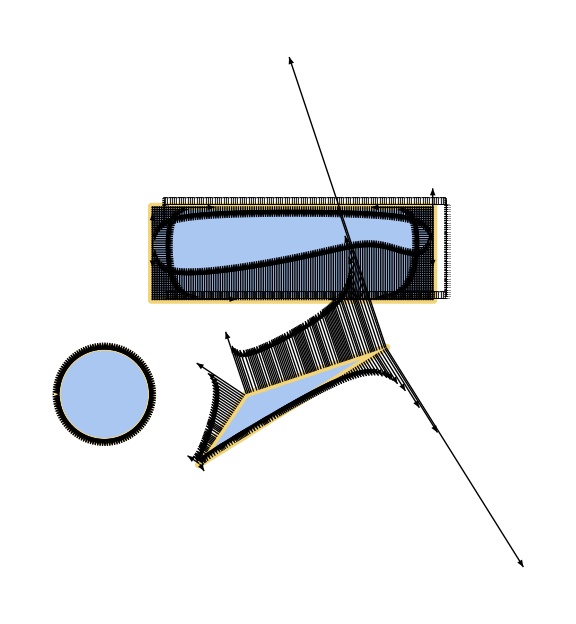

```mathematica
Show[
HighlightMesh[bMesh,0,ImageSize->Large],
Graphics[{
Arrowheads[.02],
ParallelTable[
Arrow[{
Knots[[i]],
Knots[[i]]-0.05×q[[i]]{-#[[2]],#[[1]]}/Norm[#]&[Segment[[i]]]
}],
{i,1,NEl}]}
],
Graphics[ParallelTable[Text[Style[Round[u[[i]],0.1],Black,10],Knots[[i]]+{0.3,0.1}],{i,1,NEl}]]]
```

```mathematica
(* MATRIX METHOD *)
```

```mathematica
Subscript[G, RR]=G[[RectangleInd,RectangleInd]];
Subscript[G, RT]=G[[RectangleInd,TriangleInd]];
Subscript[G, RD]=G[[RectangleInd,DiskInd]];
Subscript[G, TR]=G[[TriangleInd,RectangleInd]];
Subscript[G, TT]=G[[TriangleInd,TriangleInd]];
Subscript[G, TD]=G[[TriangleInd,DiskInd]];
Subscript[G, DR]=G[[DiskInd,RectangleInd]];
Subscript[G, DT]=G[[DiskInd,TriangleInd]];
Subscript[G, DD]=G[[DiskInd,DiskInd]];
```

```mathematica
Subscript[H, RR]=H[[RectangleInd,RectangleInd]];
Subscript[H, RT]=H[[RectangleInd,TriangleInd]];
Subscript[H, RD]=H[[RectangleInd,DiskInd]];
Subscript[H, TR]=H[[TriangleInd,RectangleInd]];
Subscript[H, TT]=H[[TriangleInd,TriangleInd]];
Subscript[H, TD]=H[[TriangleInd,DiskInd]];
Subscript[H, DR]=H[[DiskInd,RectangleInd]];
Subscript[H, DT]=H[[DiskInd,TriangleInd]];
Subscript[H, DD]=H[[DiskInd,DiskInd]];
```

```mathematica
qRv=ParallelTable[Subscript[qR, i],{i,1,Length[RectangleInd]}];
qTv=ParallelTable[Subscript[qT, i],{i,1,Length[TriangleInd]}];
qDv=ParallelTable[2,{i,1,Length[DiskInd]}];
```

```mathematica
uRv=ParallelTable[1,{i,1,Length[RectangleInd]}];
uTv=ParallelTable[Subscript[uT, i],{i,1,Length[TriangleInd]}];
uDv=ParallelTable[Subscript[uD, i],{i,1,Length[DiskInd]}];
```

```mathematica
A=ParallelTable[If[i==j,1,If[i==j-1,-1,0]],{i,1,Length[TriangleInd]-1},{j,1,Length[TriangleInd]}];
```

```mathematica
B=ParallelTable[Cross[
Append[({-#[[2]],#[[1]]}/Measure[[i]]&[Segment[[i]]]),0],
Append[Segment[[i]],0]
][[3]],{i,TriangleInd},{j,1,1}];
```

```mathematica
LeftMatrix=Join[
Join[Subscript[G, RR],Subscript[G, RT],-Subscript[H, RD],-Subscript[H, RT],2],
Join[Subscript[G, TR],Subscript[G, TT],-Subscript[H, TD],-Subscript[H, TT],2],
Join[Subscript[G, DR],Subscript[G, DT],-Subscript[H, DD],-Subscript[H, DT],2],
Join[Table[0,{i,1,1},{j,1,Length[RectangleInd]}],Transpose[B],Table[0,{i,1,1},{j,1,Length[DiskInd]+Length[TriangleInd]}],2],
Join[Table[0,{i,1,Length[TriangleInd]-1},{j,1,NEl}],A,2]
];
```

```mathematica
RightMatrix=Join[
Join[Subscript[H, RR],-Subscript[G, RD],2],
Join[Subscript[H, TR],-Subscript[G, TD],2],
Join[Subscript[H, DR],-Subscript[G, DD],2],
Table[0,{i,1,Length[LeftMatrix]-NEl},{j,1,Length[RectangleInd]+Length[DiskInd]}]
];
```

```mathematica
Charge=Join[
Table[0,{i,1,NEl}],
{-QQ/ϵ0},
Table[0,{i,1,Length[TriangleInd]-1}]
];
```

```mathematica
s=LinearSolve[LeftMatrix,RightMatrix.Join[uRv,qDv]+Charge];
```

```mathematica
qRv=s[[1;;Length[RectangleInd]]];
qTv=s[[1+Length[RectangleInd];;Length[TriangleInd]+Length[RectangleInd]]];
uDv=s[[1+Length[TriangleInd]+Length[RectangleInd];;Length[DiskInd]+Length[TriangleInd]+Length[RectangleInd]]];
uTv=s[[1+Length[DiskInd]+Length[TriangleInd]+Length[RectangleInd];;Length[TriangleInd]+Length[DiskInd]+Length[TriangleInd]+Length[RectangleInd]]];
```

```mathematica
uM=Join[uRv,uTv,uDv];
qM=Join[qRv,qTv,qDv];
```

```mathematica
Show[
HighlightMesh[bMesh,0,ImageSize->Large],
Graphics[{
Arrowheads[.02],
ParallelTable[
Arrow[{
Knots[[i]],
Knots[[i]]-0.05×qM[[i]]{-#[[2]],#[[1]]}/Norm[#]&[Segment[[i]]]
}],
{i,1,NEl}]}
],
Graphics[ParallelTable[Text[Style[Round[uM[[i]],0.1],Black,10],Knots[[i]]+{0.3,0.1}],{i,1,NEl}]]]
```

-Graphics-

```mathematica
Chop[u-uM]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Chop[q-qM]
```

{3.58661×10^-10,-2.16456×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.5072×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4.23881×10^-10,2.54744×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
uRv
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
uTv
```

{32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653,32.6653}

```mathematica
uDv
```

{23.4481,22.8435,22.2306,21.6126,20.9929,20.3751,19.7632,19.1609,18.5722,18.001,17.4513,16.927,16.4318,15.9692,15.5427,15.1553,14.8096,14.508,14.2524,14.0441,13.884,13.7723,13.7088,13.6927,13.7225,13.7966,13.9127,14.0683,14.2607,14.487,14.7443,15.0295,15.3398,15.6722,16.024,16.3925,16.7754,17.1704,17.5752,17.9879,18.4068,18.8301,19.2564,19.6842,20.1124,20.5398,20.9654,21.3883,21.8077,22.2228,22.633,23.0378,23.4366,23.8289,24.2144,24.5927,24.9634,25.3264,25.6813,26.028,26.3663,26.696,27.017,27.3293,27.6326,27.9269,28.2122,28.4884,28.7555,29.0135,29.2622,29.5018,29.7322,29.9534,30.1654,30.3683,30.562,30.7465,30.9219,31.0882,31.2454,31.3935,31.5326,31.6626,31.7836,31.8955,31.9984,32.0922,32.177,32.2527,32.3193,32.3768,32.4251,32.4641,32.4937,32.514,32.5246,32.5255,32.5165,32.4975,32.468,32.4279,32.3769,32.3145,32.2404,32.1541,32.055,31.9426,31.8163,31.6752,31.5186,31.3458,31.1559,30.9479,30.7209,30.474,30.2064,29.917,29.6052,29.2703,28.9115,28.5286,28.1213,27.6896,27.2338,26.7543,26.2519,25.7279,25.1835,24.6207,24.0414}

```mathematica
qRv
```

{-21.5167,-19.0298,-17.3636,-16.3166,-15.5898,-15.0624,-14.6687,-14.3699,-14.1416,-13.9673,-13.8356,-13.7381,-13.6687,-13.6228,-13.5968,-13.5878,-13.5936,-13.6123,-13.6426,-13.6831,-13.7329,-13.7911,-13.857,-13.93,-14.0096,-14.0952,-14.1866,-14.2833,-14.385,-14.4915,-14.6024,-14.7176,-14.8367,-14.9597,-15.0863,-15.2163,-15.3497,-15.4861,-15.6255,-15.7677,-15.9127,-16.0603,-16.2104,-16.3629,-16.5177,-16.6748,-16.8341,-16.9956,-17.1592,-17.3249,-17.4926,-17.6624,-17.8342,-18.008,-18.184,-18.3619,-18.542,-18.7242,-18.9085,-19.0949,-19.2836,-19.4744,-19.6675,-19.8628,-20.0603,-20.2601,-20.4621,-20.6662,-20.8726,-21.0809,-21.2913,-21.5035,-21.7173,-21.9326,-22.1492,-22.3666,-22.5846,-22.8027,-23.0203,-23.2369,-23.4518,-23.664,-23.8727,-24.0767,-24.2749,-24.4657,-24.6476,-24.8189,-24.9777,-25.1219,-25.2493,-25.3576,-25.4444,-25.5075,-25.5446,-25.5536,-25.5327,-25.4806,-25.3964,-25.2799,-25.1316,-24.9529,-24.7461,-24.514,-24.2607,-23.9908,-23.7097,-23.4233,-23.1381,-22.8612,-22.6001,-22.3631,-22.1591,-21.9986,-21.8942,-21.8617,-21.9225,-22.1071,-22.4631,-23.07,-24.0747,-25.8422,-28.6037,-47.6069,-44.6659,-24.0452,-20.3571,-17.8236,-16.1405,-14.9047,-13.9505,-13.187,-12.5607,-12.0372,-11.5935,-11.2136,-10.8858,-10.6014,-10.3538,-10.1381,-9.95032,-9.78736,-9.64686,-9.52697,-9.42625,-9.34368,-9.27856,-9.23052,-9.19947,-9.18568,-9.18974,-9.21266,-9.25594,-9.32168,-9.4128,-9.53331,-9.68879,-9.88714,-10.1398,-10.4641,-10.8875,-11.4569,-12.2589,-13.508,-15.3466,-26.6004,-25.7854,-14.2907,-12.2591,-10.855,-9.91679,-9.22218,-8.68023,-8.24134,-7.87616,-7.56599,-7.29824,-7.0641,-6.85715,-6.6726,-6.50677,-6.35683,-6.22048,-6.09591,-5.98161,-5.87636,-5.77912,-5.68903,-5.60535,-5.52745,-5.45479,-5.3869,-5.32336,-5.26383,-5.20798,-5.15553,-5.10624,-5.05989,-5.01627,-4.97523,-4.93658,-4.90021,-4.86596,-4.83373,-4.80342,-4.77492,-4.74815,-4.72303,-4.69949,-4.67747,-4.65689,-4.63772,-4.6199,-4.60338,-4.58812,-4.57409,-4.56125,-4.54958,-4.53904,-4.52961,-4.52128,-4.51402,-4.50781,-4.50264,-4.49851,-4.49539,-4.49329,-4.4922,-4.49211,-4.49303,-4.49496,-4.49789,-4.50185,-4.50682,-4.51283,-4.51989,-4.528,-4.53719,-4.54748,-4.55889,-4.57144,-4.58516,-4.60008,-4.61624,-4.63367,-4.65242,-4.67253,-4.69405,-4.71704,-4.74156,-4.76768,-4.79546,-4.82499,-4.85635,-4.88965,-4.92499,-4.96249,-5.00228,-5.04451,-5.08933,-5.13692,-5.18749,-5.24125,-5.29846,-5.3594,-5.42439,-5.49378,-5.56801,-5.64753,-5.73291,-5.82477,-5.92387,-6.03107,-6.14742,-6.27417,-6.41282,-6.56522,-6.73368,-6.92107,-7.1311,-7.36861,-7.64007,-7.95439,-8.32426,-8.76858,-9.31695,-10.0195,-10.9678,-12.3865,-14.4385,-26.0445,-26.8477,-15.4747,-13.6099,-12.3402,-11.5218,-10.9376,-10.5003,-10.1623,-9.8959,-9.68345,-9.51331,-9.3774,-9.27,-9.18691,-9.12505,-9.08216,-9.05654,-9.047,-9.05269,-9.07312,-9.10808,-9.1576,-9.22201,-9.30189,-9.39815,-9.51203,-9.64517,-9.79975,-9.97858,-10.1853,-10.4248,-10.7034,-11.0298,-11.4161,-11.8797,-12.4464,-13.1571,-14.0811,-15.3453,-17.2614,-20.0529,-36.1601,-37.0278}

```mathematica
qTv
```

{24.6633,18.2492,16.3315,14.9523,13.9074,13.0524,12.3223,11.6803,11.1038,10.578,10.0925,9.63999,9.21498,8.81339,8.43177,8.07525,7.67463,7.34211,7.16697,6.97159,6.80225,6.5098,6.13782,5.86862,5.72348,5.56273,5.40665,5.25452,5.12369,4.89405,4.67538,4.56559,4.44555,4.34431,4.18385,4.01701,3.94203,3.95066,3.92854,6.01787,3.52124,1.07429,0.874555,0.760427,0.625416,0.514198,0.44911,0.407552,0.381426,0.36566,0.358537,0.356598,0.355373,0.35513,0.357133,0.362727,0.3713,0.382749,0.393065,0.399518,0.407185,0.415311,0.423893,0.432908,0.442338,0.45216,0.462391,0.471706,0.489278,0.513336,0.538416,0.565015,0.5931,0.623438,0.647866,0.662026,0.678377,0.693097,0.720478,0.757468,0.795518,0.836281,0.871987,0.90028,0.930829,0.962427,0.995153,1.02904,1.06415,1.10053,1.13824,1.17735,1.21793,1.26005,1.30379,1.34925,1.39651,1.44567,1.49686,1.55018,1.60576,1.66375,1.7243,1.78756,1.85371,1.92296,1.99551,2.0716,2.15149,2.23546,2.32382,2.41688,2.5151,2.61634,2.74184,2.89285,3.05399,3.22844,3.41783,3.62414,3.8497,4.09737,4.37057,4.6735,5.01139,5.39086,5.82037,6.31021,6.87432,7.52131,8.37441,9.51271,11.0104,12.4679,13.313,15.6212,19.9187,29.1539,42.1456,110.028,130.257,63.1567,50.6022,41.6046,37.3871,35.0897,34.1378,33.1524,32.3706,31.2057,29.9422,28.9054,28.2041,27.8934,27.3032,26.5946,26.1064,25.852,25.5739,25.3077,25.0516,24.805,24.5674,24.3382,24.1164,23.9251,23.5984,23.1951,22.8146,22.5332,22.3819,22.2136,22.0678,21.815,21.4994,21.1979,20.9731,20.8513,20.7157,20.5831,20.4529,20.3256,20.2007,20.0921,19.9037,19.6684,19.4444,19.2723,19.1633,19.0485,18.9373,18.8297,18.726,18.626,18.5408,18.3943,18.2577,18.1912,18.1197,18.0546,17.9961,17.9493,17.8854,17.8431,17.8378,17.8437,17.8679,17.9147,17.9732,18.1665,18.6594,19.3524,20.0977,21.3396,27.8995}

```mathematica
qDv
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
t=SessionTime[]-t0
```

2145.598138

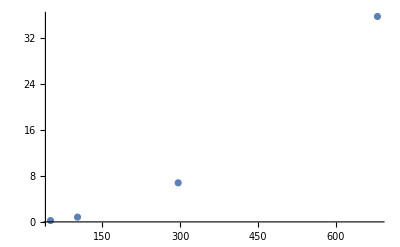

```mathematica
ListPlot[{{50,14/60},{102,50/60},{296,408/60},{680,2145/60}},PlotRange->All,Joined->False]
```